```mathematica
Clear["Global`*"];
```

## Анализ результатов работы программы

```mathematica
datatrad1 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res3\\output_data_traditional_4096.txt", "Table"];datatrad2 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res3\\output_data_traditional_8192.txt", "Table"];
datablock1 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res3\\output_data_block_4096.txt", "Table"];
datablock2 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res3\\output_data_block_8192.txt", "Table"];
```

```mathematica
data =Table[{datatrad1[[i]][[1]],
 datatrad1[[i]][[2]], (datatrad1[[1]][[2]])/(datatrad1[[i]][[2]]),
datatrad2[[i]][[2]],(datatrad2[[1]][[2]])/(datatrad2[[i]][[2]]),
datablock1[[i]][[2]], (datablock1[[1]][[2]])/(datablock1[[i]][[2]]),
datablock2[[i]][[2]],(datablock2[[1]][[2]])/(datablock2[[i]][[2]])
}, {i, 1, Length@datablock1}];

data = Prepend[ data,{"Потоки","Традиционный алгоритм,  n = 4096","Ускорение", "Традиционный алгоритм,  n = 8192","Ускорение","Блочный алгоритм, n = 4096","Ускорение","Блочный алгоритм, n = 8192","Ускорение"}];
Grid[data,Frame->All, Spacings->{1, 2}, ItemSize->{8, 2}]
```

Потоки | Традиционный алгоритм,  n = 4096 | Ускорение | Традиционный алгоритм,  n = 8192 | Ускорение | Блочный алгоритм, n = 4096 | Ускорение | Блочный алгоритм, n = 8192 | Ускорение
1 | 23.5793 | 1. | 197.355 | 1. | 15.8061 | 1. | 140.864 | 1.
2 | 12.6312 | 1.86675 | 105.811 | 1.86517 | 8.55241 | 1.84815 | 71.1455 | 1.97994
4 | 7.40453 | 3.18444 | 64.8667 | 3.04247 | 4.35046 | 3.6332 | 36.5677 | 3.85214
6 | 6.10845 | 3.86011 | 55.5035 | 3.55572 | 2.94796 | 5.36171 | 24.6798 | 5.70766
8 | 5.54501 | 4.25235 | 51.0358 | 3.86699 | 2.26398 | 6.98155 | 18.6663 | 7.54643
10 | 5.14723 | 4.58097 | 48.2393 | 4.09117 | 1.80005 | 8.78092 | 15.0188 | 9.37918
12 | 4.89782 | 4.81424 | 46.9052 | 4.20753 | 1.55197 | 10.1845 | 12.8075 | 10.9986
14 | 4.71355 | 5.00245 | 46.387 | 4.25453 | 1.38489 | 11.4133 | 11.5329 | 12.2141
16 | 4.62112 | 5.10251 | 45.586 | 4.32929 | 1.23774 | 12.7701 | 10.3945 | 13.5518
18 | 4.60683 | 5.11834 | 45.271 | 4.35941 | 1.21287 | 13.032 | 9.80296 | 14.3695

```mathematica
(*Show[
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[2]])/(data[[i]][[2]])}, {i, 2, Length@data}]], 
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[4]])/(data[[i]][[4]])}, {i, 2, Length@data}]],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[6]])/(data[[i]][[6]])}, {i, 2, Length@data}]],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[8]])/(data[[i]][[8]])}, {i, 2, Length@data}]],

PlotStyle->{Orange, Blue, Green, Red},
PlotLegends->Placed[LineLegend[{"Традиционный, n = 4096","Традиционный, n = 8192","Блочный, n = 4096","Блочный, n = 8192"}, LegendFunction->Frame], {1, 1}],

(*PlotTheme->"Scientific", *)
GridLines->Automatic,
AspectRatio-> 1/GoldenRatio,
Axes ->True,
AxesStyle->{{Arrowheads[0.025], Black},{Arrowheads[0.03], Black}},AxesLabel->{Style["n, Threads",Black,16, FontFamily->"Times"],Style["t_1/t_n",Black,16, FontFamily->"Times"]},LabelStyle->Directive[Black,14, FontFamily->"Times"],
ImageSize->{800, 500},PlotRange->All,
PlotLabel->"График зависимости усконения от потоков" ]*)

Show[
Plot[x, {x, 1, 18}, PlotStyle->Black, PlotLegends->{"Прямая y[x] = x"}],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[2]])/(data[[i]][[2]])},{i,2,Length@data}],PlotStyle->Orange,PlotLegends->{"Традиционный, n = 4096"}],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[4]])/(data[[i]][[4]])},{i,2,Length@data}],PlotStyle->Blue,PlotLegends->{"Традиционный, n = 8192"}],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[6]])/(data[[i]][[6]])},{i,2,Length@data}],PlotStyle->Green,PlotLegends->{"Блочный, n = 4096"}],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[8]])/(data[[i]][[8]])},{i,2,Length@data}],PlotStyle->Red,PlotLegends->{"Блочный, n = 8192"}],


GridLines->Automatic,AspectRatio->1/GoldenRatio,Axes->True,AxesStyle->{{Arrowheads[0.025],Black},{Arrowheads[0.03],Black}},
AxesLabel->{Style["n, Threads",Black,16,FontFamily->"Times"],Style["\!\(\*SubscriptBox[\(t\), \(1\)]\)/\!\(\*SubscriptBox[\(t\), \(n\)]\)",Black,16,FontFamily->"Times"]},LabelStyle->Directive[Black,14,FontFamily->"Times"],ImageSize->{800,500},PlotRange->All,PlotLabel->"График зависимости усконения от потоков"]
```

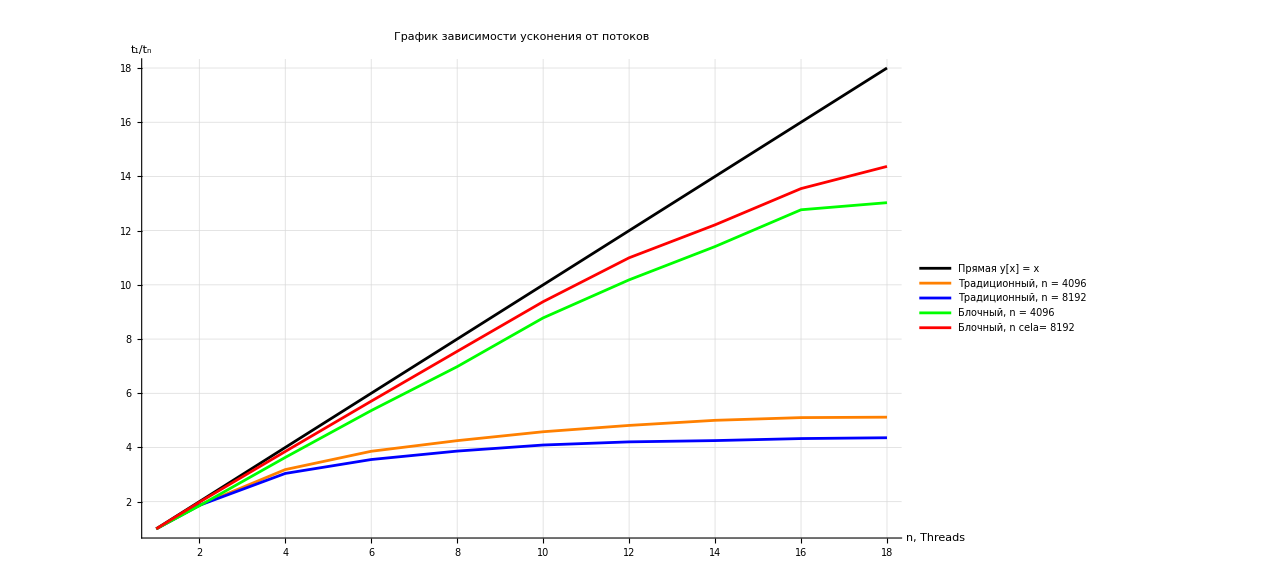

```mathematica
data[[2]][[3]]
```

1.